```mathematica
Quit
Clear[*]
```

```mathematica
data={{0,0},{1,3},{3,2},{5,2},{4,1},{10,-3}}
```

{{0,0},{1,3},{3,2},{5,2},{4,1},{10,-3}}

```mathematica
sp=Interpolation[data,InterpolationOrder->2]
```

InterpolatingFunction[…]

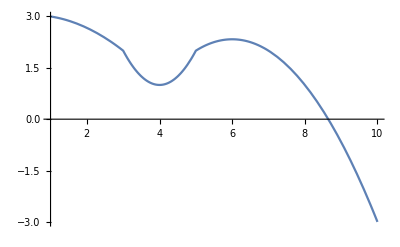

```mathematica
Plot[sp[x],{x,1,10}]
```

```mathematica
sp1=Interpolation[data,Method->"Spline"]
```

InterpolatingFunction[…]

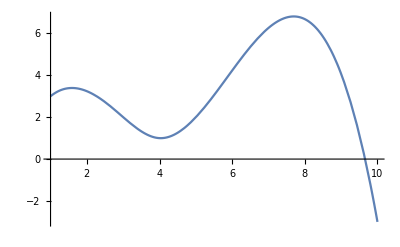

```mathematica
Plot[sp1[x],{x,1,10}]
```

```mathematica
sp2=Interpolation[data,Method->"Hermite"]
```

InterpolatingFunction[…]

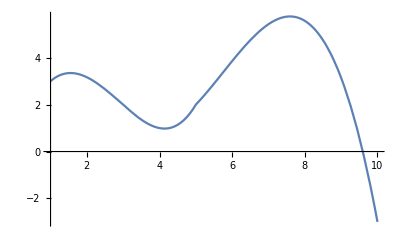

```mathematica
Plot[sp2[x], {x,1,10}]
```

```mathematica
c[x_]:=InterpolatingPolynomial[data,x]
```

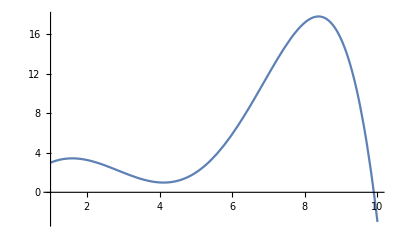

```mathematica
Plot[c[x], {x,1,10}]
```

```mathematica
Clear[*]
```

```mathematica
A={{1,2},{3,4}}
```

{{1,2},{3,4}}

```mathematica
A//MatrixForm
```

(1 | 2
3 | 4)

```mathematica
B={{5,6}}
```

{{5,6}}

```mathematica
B//MatrixForm
```

(5 | 6)

```mathematica
result=Transpose[Join[Transpose[A],B]]
```

{{1,2,5},{3,4,6}}

```mathematica
result//MatrixForm
```

(1 | 2 | 5
3 | 4 | 6)

```mathematica
clear[*]
```

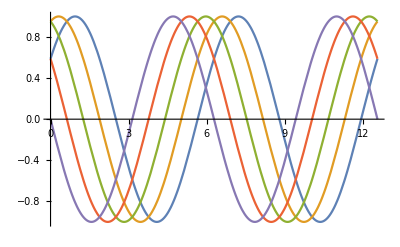

```mathematica
Plot[Evaluate[Table[Sin[x+a],{a,π/5,π,π/5}]],{x,0,4*π}]
```

```mathematica
Plot[Evaluate[Table[Sin[x+a],{a,π/5,π,π/5}]],{x,0,4*π},PlotLegends-> Automatic]
```

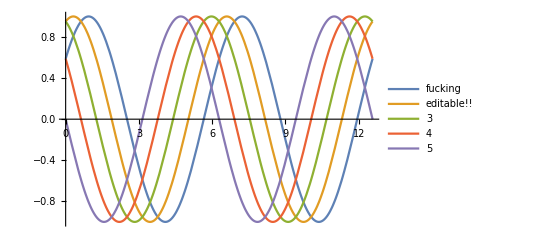

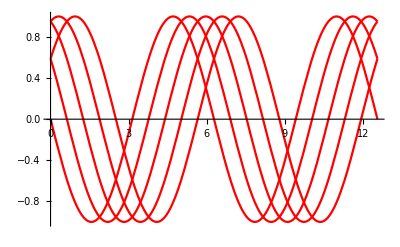

```mathematica
Plot[Evaluate[Table[Sin[x+a],{a,π/5,π,π/5}]],{x,0,4*π},PlotLegends-> "Expressions",PlotStyle->{RGBColor[1,0,0]}]
```

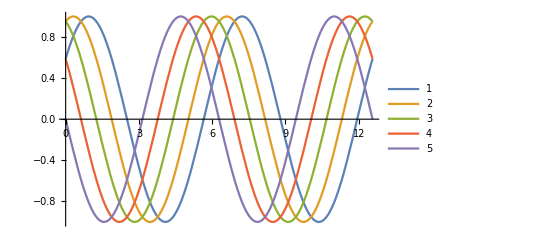

```mathematica
Plot[Evaluate[Table[Sin[x+a],{a,π/5,π,π/5}]],{x,0,4*π},PlotLegends-> {1,2,3,4,5}]
```

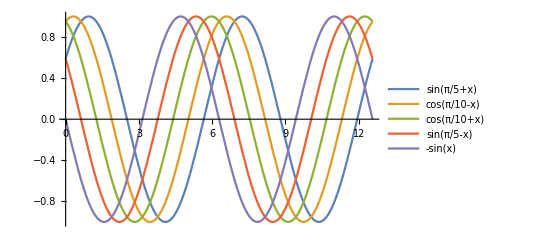

```mathematica
Plot[Evaluate[Table[Sin[x+a],{a,π/5,π,π/5}]],{x,0,4*π},PlotLegends-> Placed["Expressions",Below]]
```

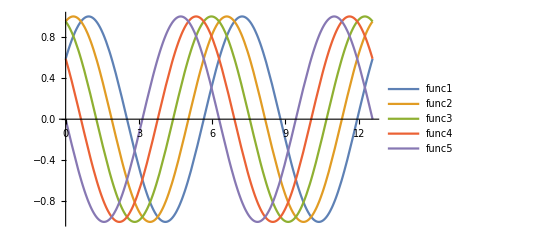

```mathematica
Plot[Evaluate[Table[Sin[x+a],{a,π/5,π,π/5}]],{x,0,4*π},PlotLegends-> Placed[{"func1","func2","func3","func4","func5"},Right]]
```

```mathematica
Plot[Evaluate[Table[Sin[x+a],{a,π/5,π,π/5}]],{x,0,4*π},PlotLegends-> Placed[Automatic,Below]]
```

-Graphics-

```mathematica
Plot[Evaluate[Table[Sin[x+a],{a,π/5,π,π/5}]],{x,0,4*π},PlotLabels-> Automatic,PlotStyle->{Red,Green,Blue,Black,Yellow}]
```

-Graphics-

```mathematica
Plot[Evaluate[Table[Sin[x+a],{a,π/5,π,π/5}]],{x,0,4*π},PlotLabels-> "Expressions"]
```

-Graphics-

```mathematica
Plot[Evaluate[Table[Sin[x+a],{a,π/5,π,π/5}]],{x,0,4*π},PlotLabels-> "Expressions",PlotPoints->10]
```

-Graphics-

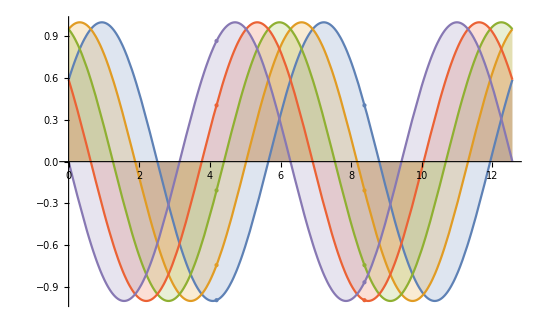

```mathematica
Plot[Evaluate[Table[Sin[x+a],{a,π/5,π,π/5}]],{x,0,4π},Filling->Axis,Mesh->2]
```

```mathematica
func1[x_,y_]:=x^2+y
```

```mathematica
Plot3D[func1[x,y],{x,-5,5},{y,-5,5},Mesh->1,PlotPoints->10]
```

-Graphics3D-

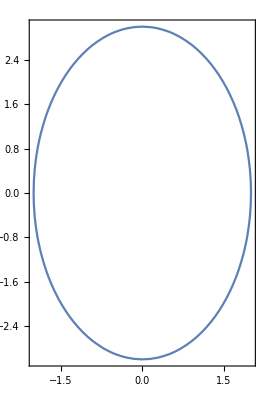

```mathematica
ContourPlot[x^2/4+y^2/9==1,{x,-2,2},{y,-3,3},AspectRatio->Automatic]
```

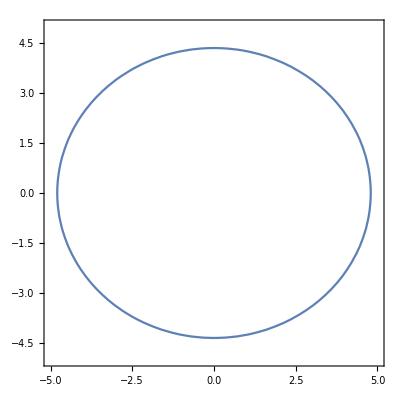

```mathematica
ContourPlot[x^2/23+y^2/19==1,{x,-5,5},{y,-5,5},AspectRatio->Automatic]
```

```mathematica
A={{1,2},{3,4}}
```

{{1,2},{3,4}}

```mathematica
A^2
```

{{1,4},{9,16}}

```mathematica
A^2//MatrixForm
```

(1 | 4
9 | 16)

```mathematica
MatrixPower[A^2,2]
```

{{37,68},{153,292}}

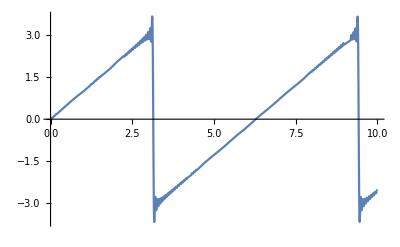

```mathematica
Plot[Evaluate[FourierTrigSeries[x,x,100, FourierParameters->{1,1}]],{x,0,10}]
```

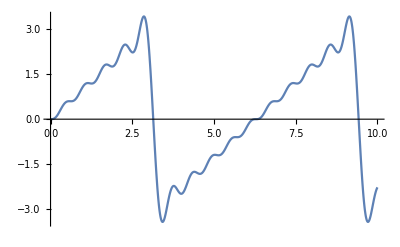

```mathematica
Plot[Evaluate[FourierTrigSeries[x,x,10, FourierParameters->{1,1}]],{x,0,10}]
```

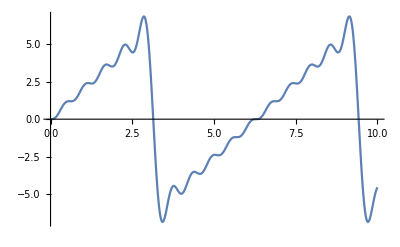

```mathematica
Plot[Evaluate[FourierTrigSeries[x,x,10, FourierParameters->{2,1}]],{x,0,10}]
```

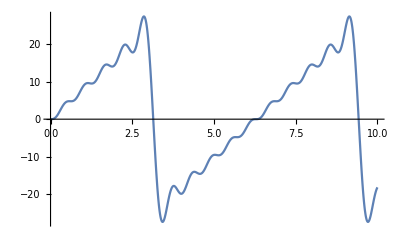

```mathematica
Plot[Evaluate[FourierTrigSeries[x,x,10, FourierParameters->{4,1}]],{x,0,10}]
```

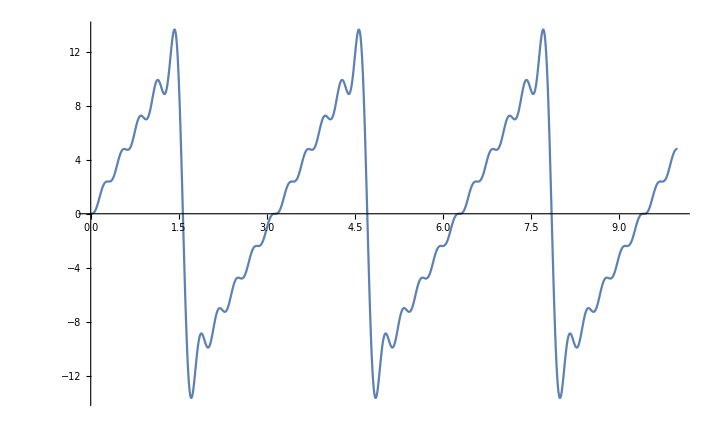

```mathematica
Plot[Evaluate[FourierTrigSeries[x,x,10, FourierParameters->{4,2}]],{x,0,10}]
```

```mathematica
DSolve[{y''[t]+4y'[t]+7y[t]==DiracDelta[t],y[0]==3,y'[0]==5},y[t],t]
```

{{y[t]→1/3 ⅇ^(-2 t) (9 Cos[√3 t]+11 √3 Sin[√3 t]-√3 HeavisideTheta[0] Sin[√3 t]+√3 HeavisideTheta[t] Sin[√3 t])}}

```mathematica
Quit
```

```mathematica
Clear[*]
```

```mathematica
DSolve[{3y''[t]+5y'[t]+2y[t]==UnitStep[t],y[0]==1,y'[0]==1},y[t],t]
```

{{y[t]→ⅇ^-t (-5+6 ⅇ^(t/3))+(-ⅇ^-t (-5+6 ⅇ^(t/3))+1/2 ⅇ^-t (-8+9 ⅇ^(t/3)+ⅇ^t)) UnitStep[t]}}

```mathematica
Clear[*]
```

```mathematica
s1=y''[t]+y[t]==0
```

y[t]+y''[t]==0

```mathematica
LaplaceTransform[s1,t,s]
```

LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]-s y[0]-y'[0]==0

```mathematica
%
```

LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]-s y[0]-y'[0]==0

```mathematica
Solve[%,LaplaceTransform[y[t],t,s]]
```

{{LaplaceTransform[y[t],t,s]→(s y[0]+y'[0])/(1+s^2)}}

```mathematica
%[[1]]/.{y[0]->1,y'[0]->-1}
```

{LaplaceTransform[y[t],t,s]→(-1+s)/(1+s^2)}

```mathematica
InverseLaplaceTransform[LaplaceTransform[y[t],t,s]/.%,s,t]
```

Cos[t]-Sin[t]

```mathematica
Quit
```

```mathematica
LaplaceTransform[{y''[t]+7y'[t]+y[t]==DiracDelta[t]},t,s]
```

{LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]+7 (s LaplaceTransform[y[t],t,s]-y[0])-s y[0]-y'[0]==1}

```mathematica
Solve[%,LaplaceTransform[y[t],t,s]]
```

{{LaplaceTransform[y[t],t,s]→(1+7 y[0]+s y[0]+y'[0])/(1+7 s+s^2)}}

```mathematica
%[[1]]/.{y[0]->2,y'[0]->1}
```

{LaplaceTransform[y[t],t,s]→(16+2 s)/(1+7 s+s^2)}

```mathematica
InverseLaplaceTransform[LaplaceTransform[y[t],t,s]/.%,s,t]
```

1/(√5)(-3 ⅇ^((-7/2-(3 √5)/2) t)+√5 ⅇ^((-7/2-(3 √5)/2) t)+3 ⅇ^((-7/2+(3 √5)/2) t)+√5 ⅇ^((-7/2+(3 √5)/2) t))

```mathematica
Quit
```

```mathematica
LaplaceTransform[{y''[t]+7y'[t]+y[t]==DiracDelta[t]},t,s]
```

{LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]+7 (s LaplaceTransform[y[t],t,s]-y[0])-s y[0]-y'[0]==1}

```mathematica
sol1=Solve[%,LaplaceTransform[y[t],t,s]]
```

{{LaplaceTransform[y[t],t,s]→(1+7 y[0]+s y[0]+y'[0])/(1+7 s+s^2)}}

```mathematica
%[[1]]/.{y[0]->a,y'[0]->b}
```

{LaplaceTransform[y[t],t,s]→(1+7 a+b+a s)/(1+7 s+s^2)}

```mathematica
solution=InverseLaplaceTransform[LaplaceTransform[y[t],t,s]/.%,s,t]//Simplify
```

1/(6 √5)ⅇ^(-1/2 (7+3 √5) t) (2 (1+b) (-1+ⅇ^(3 √5 t))+a (-7+3 √5+(7+3 √5) ⅇ^(3 √5 t)))

```mathematica
Solve[{(%/.t->1)==3,(D[%,t]/.t->2)==1},{a,b}]//Simplify
```

{{a→(-2 √5 ⅇ^7-3 (15+7 √5) ⅇ^(7/2-(3 √5)/2)+2 √5 ⅇ^(7+3 √5)+3 (-15+7 √5) ⅇ^(7/2+(9 √5)/2))/(-15-7 √5+(-15+7 √5) ⅇ^(3 √5)),b→(ⅇ^(-(3 √5)/2) (6 √5 ⅇ^(7/2)+(15+7 √5) ⅇ^((3 √5)/2)+(15-7 √5) ⅇ^((9 √5)/2)+(-15+7 √5) ⅇ^(7+(3 √5)/2)-(15+7 √5) ⅇ^(7+(9 √5)/2)-6 √5 ⅇ^(7/2+6 √5)))/(-15-7 √5+(-15+7 √5) ⅇ^(3 √5))}}

```mathematica
solution/.%[[1]]
```

1/(6 √5)ⅇ^(-1/2 (7+3 √5) t) (((-2 √5 ⅇ^7-3 (15+7 √5) ⅇ^(7/2-(3 √5)/2)+2 √5 ⅇ^(7+3 √5)+3 (-15+7 √5) ⅇ^(7/2+(9 √5)/2)) (-7+3 √5+(7+3 √5) ⅇ^(3 √5 t)))/(-15-7 √5+(-15+7 √5) ⅇ^(3 √5))+2 (-1+ⅇ^(3 √5 t)) (1+(ⅇ^(-(3 √5)/2) (6 √5 ⅇ^(7/2)+(15+7 √5) ⅇ^((3 √5)/2)+(15-7 √5) ⅇ^((9 √5)/2)+(-15+7 √5) ⅇ^(7+(3 √5)/2)-(15+7 √5) ⅇ^(7+(9 √5)/2)-6 √5 ⅇ^(7/2+6 √5)))/(-15-7 √5+(-15+7 √5) ⅇ^(3 √5))))

```mathematica
DSolve[{y''[t]+7y'[t]+y[t]==DiracDelta[t],y[1]==3,y'[2]==1},y[t],t] //Simplify
```

{{y[t]→(ⅇ^(1/2 (-3 √5-(7+3 √5) t)) ((15+7 √5) ⅇ^((3 √5)/2)+(15-7 √5) ⅇ^((9 √5)/2)-30 ⅇ^(7+(9 √5)/2)+45 (-7+3 √5) ⅇ^(7/2+6 √5)-(15+7 √5) ⅇ^(3/2 √5 (1+2 t))+(-15+7 √5) ⅇ^(3/2 √5 (3+2 t))+45 (7+3 √5) ⅇ^(7/2+3 √5 t)+30 ⅇ^(7+(3 √5)/2+3 √5 t)-ⅇ^((3 √5)/2) (-15-7 √5+(-15+7 √5) ⅇ^(3 √5)) (-1+ⅇ^(3 √5 t)) HeavisideTheta[t]))/(15 (7+3 √5+(-7+3 √5) ⅇ^(3 √5)))}}

```mathematica
Quit
```

```mathematica
DSolve[{y''[t]+4y'[t]+7y[t]==DiracDelta[t],y[1]==1,y'[2]==2},y[t],t]//Simplify
```

{{y[t]→(ⅇ^(-2 t) (6 ⅇ^2 Cos[√3 (-3+t)]-12 Cos[√3 (-2+t)]+24 ⅇ^4 Cos[√3 (-2+t)]-42 ⅇ^2 Cos[√3 (-1+t)]-24 ⅇ^4 Cos[√3 t]+12 Cos[√3 (2+t)]-24 √3 ⅇ^2 Sin[√3 (-3+t)]-√3 Sin[√3 (-2+t)]-12 √3 ⅇ^4 Sin[√3 (-2+t)]+14 √3 Sin[√3 t]-12 √3 ⅇ^4 Sin[√3 t]-√3 Sin[√3 (2+t)]+HeavisideTheta[t] (12 Cos[√3 (-2+t)]-12 Cos[√3 (2+t)]+√3 (Sin[√3 (-2+t)]-14 Sin[√3 t]+Sin[√3 (2+t)]))))/(6 (-7+Cos[2 √3]+4 √3 Sin[2 √3]))}}

```mathematica
Clear[*]
```

```mathematica
LaplaceTransform[{y''[t]+4y'[t]+7y[t]==DiracDelta[t]},t,s]
```

{7 LaplaceTransform[y[t],t,s]+s^2 LaplaceTransform[y[t],t,s]+4 (s LaplaceTransform[y[t],t,s]-y[0])-s y[0]-y'[0]==1}

```mathematica
Solve[%,LaplaceTransform[y[t],t,s]]
```

{{LaplaceTransform[y[t],t,s]→(1+4 y[0]+s y[0]+y'[0])/(7+4 s+s^2)}}

```mathematica
%[[1]]/.{y[0]->a,y'[0]->b}
```

{LaplaceTransform[y[t],t,s]→(1+4 a+b+a s)/(7+4 s+s^2)}

```mathematica
solution=%[[1]]/.{y[0]->a,y'[0]->b}
```

LaplaceTransform[y[t],t,s]→(1+4 a+b+a s)/(7+4 s+s^2)

```mathematica
solution
```

LaplaceTransform[y[t],t,s]→(1+4 a+b+a s)/(7+4 s+s^2)

```mathematica
InverseLaplaceTransform[LaplaceTransform[y[t],t,s]/.solution,s,t]
```

1/(√3)ⅇ^(-2 t) (√3 a Cos[√3 t]+Sin[√3 t]+2 a Sin[√3 t]+b Sin[√3 t])

```mathematica
Solve[{(%/.t->1)==1,(D[%,t]/.t->2)==2},{a,b}]//Simplify
```

{{a→(ⅇ^2 (-3 Cos[2 √3]+2 √3 ⅇ^2 Sin[√3]+2 √3 Sin[2 √3]))/(-3 Cos[√3]+2 √3 Sin[√3]),b→(-3 Cos[√3]+2 √3 Sin[√3]+ⅇ^4 (6 Cos[√3]+4 √3 Sin[√3])+7 √3 ⅇ^2 Sin[2 √3])/(3 Cos[√3]-2 √3 Sin[√3])}}

ReplaceAll::reps: {a,b} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

LaplaceTransform[y[t],t,s]→(1+4 a+b+a s)/(7+4 s+s^2)/.{a,b}